```mathematica
c=ToExpression[Get["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/FigsourceFiles2019/output/figuretsnecorstexPink.nb"][[1,1,1,1]]];a=ToExpression[Get["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/FigsourceFiles2019/output/6-Figure6_increasing.nb"][[1,1,1,1]]];
b=ToExpression[Get["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/FigsourceFiles2019/output/6-Figure6_decreasing.nb"][[1,1,1,1]]];
```

```mathematica
ccdList={0,1,1.25,1.5,1.75,2.5}
ccdList={0,1,1.25,1.5,1.75,2.5}
cL[x_,ccdList_]:=Flatten[If[(#[[1]]≤x)&&(x<#[[2]]),Position[Partition[ccdList,2,1],#],{}]&/@Partition[ccdList,2,1]]
cL[#,ccdList]&/@ccdList


coloB=Table[Blend[{ColorData["ThermometerColors"][0.15],Lighter[Pink,0.75]},i],{i,0,1.15,0.25}]

col[x_]:=Reverse[coloB][[x]]
```

{0,1,1.25,1.5,1.75,2.5}

{0,1,1.25,1.5,1.75,2.5}

{{1},{2},{3},{4},{5},{}}

{RGBColor[0.3536047, 0.46289399999999997, 0.9223703],RGBColor[0.515203525, 0.5659204999999999, 0.910527725],RGBColor[0.67680235, 0.668947, 0.8986851499999999],RGBColor[0.838401175, 0.7719735, 0.886842575],RGBColor[1., 0.875, 0.875]}

{RGBColor[0.3536047, 0.46289399999999997, 0.9223703],RGBColor[0.67680235, 0.668947, 0.8986851499999999],RGBColor[1., 0.875, 0.875]}

```mathematica
legen=SwatchLegend[coloB,Reverse[{0,1,1.25,1.5,1.75,2}](*{"3.0","2.5","2.0","1.5","1.0","0.0"}*),LegendLayout->"Column",LegendMarkerSize->15,LegendLabel->Placed["Cell cycle duration, Γ hrs",Right,Rotate[Style[#,16],-90Degree]&]]
```

```mathematica
legen=SwatchLegend[coloB,Reverse[{0,1,1.25,1.5,1.75,2,">2"}](*{"3.0","2.5","2.0","1.5","1.0","0.0"}*),LegendLayout->"Column",LegendMarkerSize->15,LegendLabel->Placed["Cell cycle duration, Γ hrs",Right,Rotate[Style[#,16],-90Degree]&]]
```

```mathematica
legen2=SwatchLegend[coloB[[{1,3,5}]],{Style["Slow",15,"Helvetica"],Style["Medium",15,"Helvetica"],Style["Fast",15,"Helvetica"]}(*{"3.0","2.5","2.0","1.5","1.0","0.0"}*),LegendLayout->"Column",LegendMarkerSize->15,LegendLabel->Placed["Relative Cell cycle duration",Right,Rotate[Style[#,16],-90Degree]&]]
```

```mathematica
c1={Show[#,BaseStyle->25],Style[ "→",42,Black,Bold]}&/@c;
c1[[Length[c1],2]]="";
pc=Panel[TableForm[{Flatten[{c1,legen2}]}],Style["C",30,Black,Bold],Appearance->"Frameless",Background->White];
```

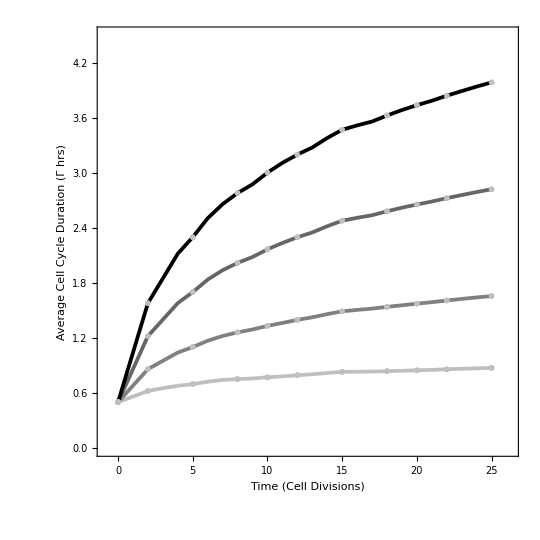
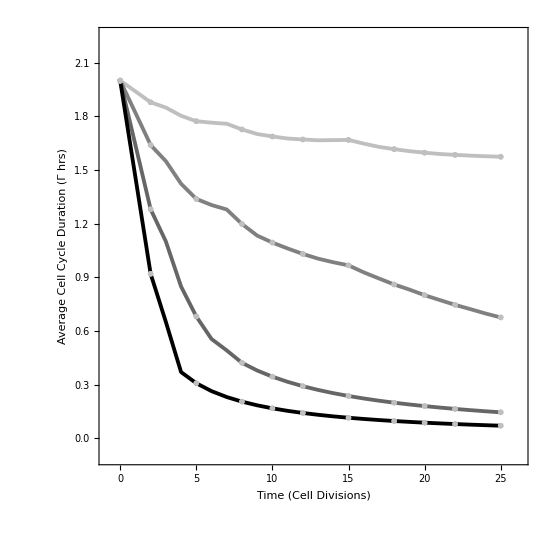
-Graphics-A |    |   |    |   | -Graphics-B | 
-Graphics- | → | -Graphics- | → | -Graphics- | → | -Graphics- |  | C

```mathematica
tad=TableForm[{TableForm[{{Panel[Show[a,BaseStyle->25],Style["A",30,Black,Bold],Appearance->"Frameless",Background->White],"  "," ","  "," ",Panel[Show[b,BaseStyle->25],Style["B",30,Black,Bold],Appearance->"Frameless",Background->White],legen}}],pc},TableAlignments->Left]
```

```mathematica
Export["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/submission01-2019-09/6-Figure-6-ims_cortexA-C.pdf",tad];
```